# NNLayout464ii Programming and Testing

## Re-formatting 464ii Layout for new Scala Nounou

```mathematica
oldLayout={{-1,457,450,442,434,426,417,407,397,387,376,364,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{463,456,449,441,433,425,416,406,396,386,375,363,352,341,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{462,455,448,440,432,424,415,405,395,385,374,362,351,340,329,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{461,454,447,439,431,423,414,404,394,384,373,361,350,339,328,317,-1,-1,-1,-1,-1,-1,-1,-1,-1},{460,453,446,438,430,422,413,403,393,383,372,360,349,338,327,316,306,-1,-1,-1,-1,-1,-1,-1,-1},{459,452,445,437,429,421,412,402,392,382,371,359,348,337,326,315,305,296,-1,-1,-1,-1,-1,-1,-1},{458,451,444,436,428,420,411,401,391,381,370,358,347,336,325,314,304,295,286,-1,-1,-1,-1,468,-1},{231,226,443,435,427,419,410,400,390,380,369,357,346,335,324,313,303,294,285,276,-1,-1,-1,469,464},{230,225,219,212,204,418,409,399,389,379,368,356,345,334,323,312,302,293,284,275,267,-1,-1,470,465},{229,224,218,211,203,195,408,398,388,378,367,355,344,333,322,311,301,292,283,274,266,259,-1,471,466},{228,223,217,210,202,194,186,177,167,377,366,354,343,332,321,310,300,291,282,273,265,258,251,-1,467},{227,222,216,209,201,193,185,176,166,156,365,353,342,331,320,309,299,290,281,272,264,257,250,243,-1},{-1,221,215,208,200,192,184,175,165,155,145,134,122,330,319,308,298,289,280,271,263,256,249,242,-1},{-1,220,214,207,199,191,183,174,164,154,144,133,121,110,318,307,297,288,279,270,262,255,248,241,236},{-1,-1,213,206,198,190,182,173,163,153,143,132,120,109,98,87,76,287,278,269,261,254,247,240,235},{-1,-1,-1,205,197,189,181,172,162,152,142,131,119,108,97,86,75,65,277,268,260,253,246,239,234},{-1,-1,-1,-1,196,188,180,171,161,151,141,130,118,107,96,85,74,64,55,46,37,252,245,238,233},{-1,-1,-1,-1,-1,187,179,170,160,150,140,129,117,106,95,84,73,63,54,45,36,28,244,237,232},{-1,-1,-1,-1,-1,-1,178,169,159,149,139,128,116,105,94,83,72,62,53,44,35,27,20,13,6},{-1,-1,-1,-1,-1,-1,-1,168,158,148,138,127,115,104,93,82,71,61,52,43,34,26,19,12,5},{-1,-1,-1,-1,-1,-1,-1,-1,157,147,137,126,114,103,92,81,70,60,51,42,33,25,18,11,4},{-1,-1,-1,-1,-1,-1,-1,-1,-1,146,136,125,113,102,91,80,69,59,50,41,32,24,17,10,3},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,135,124,112,101,90,79,68,58,49,40,31,23,16,9,2},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,123,111,100,89,78,67,57,48,39,30,22,15,8,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,99,88,77,66,56,47,38,29,21,14,7,0}};
```

```mathematica
Dimensions[oldLayout]
```

{25,25}

```mathematica
oldLayout//TableForm
```

-1 | 457 | 450 | 442 | 434 | 426 | 417 | 407 | 397 | 387 | 376 | 364 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
463 | 456 | 449 | 441 | 433 | 425 | 416 | 406 | 396 | 386 | 375 | 363 | 352 | 341 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
462 | 455 | 448 | 440 | 432 | 424 | 415 | 405 | 395 | 385 | 374 | 362 | 351 | 340 | 329 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
461 | 454 | 447 | 439 | 431 | 423 | 414 | 404 | 394 | 384 | 373 | 361 | 350 | 339 | 328 | 317 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
460 | 453 | 446 | 438 | 430 | 422 | 413 | 403 | 393 | 383 | 372 | 360 | 349 | 338 | 327 | 316 | 306 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
459 | 452 | 445 | 437 | 429 | 421 | 412 | 402 | 392 | 382 | 371 | 359 | 348 | 337 | 326 | 315 | 305 | 296 | -1 | -1 | -1 | -1 | -1 | -1 | -1
458 | 451 | 444 | 436 | 428 | 420 | 411 | 401 | 391 | 381 | 370 | 358 | 347 | 336 | 325 | 314 | 304 | 295 | 286 | -1 | -1 | -1 | -1 | 468 | -1
231 | 226 | 443 | 435 | 427 | 419 | 410 | 400 | 390 | 380 | 369 | 357 | 346 | 335 | 324 | 313 | 303 | 294 | 285 | 276 | -1 | -1 | -1 | 469 | 464
230 | 225 | 219 | 212 | 204 | 418 | 409 | 399 | 389 | 379 | 368 | 356 | 345 | 334 | 323 | 312 | 302 | 293 | 284 | 275 | 267 | -1 | -1 | 470 | 465
229 | 224 | 218 | 211 | 203 | 195 | 408 | 398 | 388 | 378 | 367 | 355 | 344 | 333 | 322 | 311 | 301 | 292 | 283 | 274 | 266 | 259 | -1 | 471 | 466
228 | 223 | 217 | 210 | 202 | 194 | 186 | 177 | 167 | 377 | 366 | 354 | 343 | 332 | 321 | 310 | 300 | 291 | 282 | 273 | 265 | 258 | 251 | -1 | 467
227 | 222 | 216 | 209 | 201 | 193 | 185 | 176 | 166 | 156 | 365 | 353 | 342 | 331 | 320 | 309 | 299 | 290 | 281 | 272 | 264 | 257 | 250 | 243 | -1
-1 | 221 | 215 | 208 | 200 | 192 | 184 | 175 | 165 | 155 | 145 | 134 | 122 | 330 | 319 | 308 | 298 | 289 | 280 | 271 | 263 | 256 | 249 | 242 | -1
-1 | 220 | 214 | 207 | 199 | 191 | 183 | 174 | 164 | 154 | 144 | 133 | 121 | 110 | 318 | 307 | 297 | 288 | 279 | 270 | 262 | 255 | 248 | 241 | 236
-1 | -1 | 213 | 206 | 198 | 190 | 182 | 173 | 163 | 153 | 143 | 132 | 120 | 109 | 98 | 87 | 76 | 287 | 278 | 269 | 261 | 254 | 247 | 240 | 235
-1 | -1 | -1 | 205 | 197 | 189 | 181 | 172 | 162 | 152 | 142 | 131 | 119 | 108 | 97 | 86 | 75 | 65 | 277 | 268 | 260 | 253 | 246 | 239 | 234
-1 | -1 | -1 | -1 | 196 | 188 | 180 | 171 | 161 | 151 | 141 | 130 | 118 | 107 | 96 | 85 | 74 | 64 | 55 | 46 | 37 | 252 | 245 | 238 | 233
-1 | -1 | -1 | -1 | -1 | 187 | 179 | 170 | 160 | 150 | 140 | 129 | 117 | 106 | 95 | 84 | 73 | 63 | 54 | 45 | 36 | 28 | 244 | 237 | 232
-1 | -1 | -1 | -1 | -1 | -1 | 178 | 169 | 159 | 149 | 139 | 128 | 116 | 105 | 94 | 83 | 72 | 62 | 53 | 44 | 35 | 27 | 20 | 13 | 6
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 168 | 158 | 148 | 138 | 127 | 115 | 104 | 93 | 82 | 71 | 61 | 52 | 43 | 34 | 26 | 19 | 12 | 5
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 157 | 147 | 137 | 126 | 114 | 103 | 92 | 81 | 70 | 60 | 51 | 42 | 33 | 25 | 18 | 11 | 4
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 146 | 136 | 125 | 113 | 102 | 91 | 80 | 69 | 59 | 50 | 41 | 32 | 24 | 17 | 10 | 3
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 135 | 124 | 112 | 101 | 90 | 79 | 68 | 58 | 49 | 40 | 31 | 23 | 16 | 9 | 2
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 123 | 111 | 100 | 89 | 78 | 67 | 57 | 48 | 39 | 30 | 22 | 15 | 8 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 99 | 88 | 77 | 66 | 56 | 47 | 38 | 29 | 21 | 14 | 7 | 0

```mathematica
Reverse[Transpose[oldLayout]]//TableForm
```

-1 | -1 | -1 | -1 | -1 | -1 | -1 | 464 | 465 | 466 | 467 | -1 | -1 | 236 | 235 | 234 | 233 | 232 | 6 | 5 | 4 | 3 | 2 | 1 | 0
-1 | -1 | -1 | -1 | -1 | -1 | 468 | 469 | 470 | 471 | -1 | 243 | 242 | 241 | 240 | 239 | 238 | 237 | 13 | 12 | 11 | 10 | 9 | 8 | 7
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 251 | 250 | 249 | 248 | 247 | 246 | 245 | 244 | 20 | 19 | 18 | 17 | 16 | 15 | 14
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 259 | 258 | 257 | 256 | 255 | 254 | 253 | 252 | 28 | 27 | 26 | 25 | 24 | 23 | 22 | 21
-1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 267 | 266 | 265 | 264 | 263 | 262 | 261 | 260 | 37 | 36 | 35 | 34 | 33 | 32 | 31 | 30 | 29
-1 | -1 | -1 | -1 | -1 | -1 | -1 | 276 | 275 | 274 | 273 | 272 | 271 | 270 | 269 | 268 | 46 | 45 | 44 | 43 | 42 | 41 | 40 | 39 | 38
-1 | -1 | -1 | -1 | -1 | -1 | 286 | 285 | 284 | 283 | 282 | 281 | 280 | 279 | 278 | 277 | 55 | 54 | 53 | 52 | 51 | 50 | 49 | 48 | 47
-1 | -1 | -1 | -1 | -1 | 296 | 295 | 294 | 293 | 292 | 291 | 290 | 289 | 288 | 287 | 65 | 64 | 63 | 62 | 61 | 60 | 59 | 58 | 57 | 56
-1 | -1 | -1 | -1 | 306 | 305 | 304 | 303 | 302 | 301 | 300 | 299 | 298 | 297 | 76 | 75 | 74 | 73 | 72 | 71 | 70 | 69 | 68 | 67 | 66
-1 | -1 | -1 | 317 | 316 | 315 | 314 | 313 | 312 | 311 | 310 | 309 | 308 | 307 | 87 | 86 | 85 | 84 | 83 | 82 | 81 | 80 | 79 | 78 | 77
-1 | -1 | 329 | 328 | 327 | 326 | 325 | 324 | 323 | 322 | 321 | 320 | 319 | 318 | 98 | 97 | 96 | 95 | 94 | 93 | 92 | 91 | 90 | 89 | 88
-1 | 341 | 340 | 339 | 338 | 337 | 336 | 335 | 334 | 333 | 332 | 331 | 330 | 110 | 109 | 108 | 107 | 106 | 105 | 104 | 103 | 102 | 101 | 100 | 99
-1 | 352 | 351 | 350 | 349 | 348 | 347 | 346 | 345 | 344 | 343 | 342 | 122 | 121 | 120 | 119 | 118 | 117 | 116 | 115 | 114 | 113 | 112 | 111 | -1
364 | 363 | 362 | 361 | 360 | 359 | 358 | 357 | 356 | 355 | 354 | 353 | 134 | 133 | 132 | 131 | 130 | 129 | 128 | 127 | 126 | 125 | 124 | 123 | -1
376 | 375 | 374 | 373 | 372 | 371 | 370 | 369 | 368 | 367 | 366 | 365 | 145 | 144 | 143 | 142 | 141 | 140 | 139 | 138 | 137 | 136 | 135 | -1 | -1
387 | 386 | 385 | 384 | 383 | 382 | 381 | 380 | 379 | 378 | 377 | 156 | 155 | 154 | 153 | 152 | 151 | 150 | 149 | 148 | 147 | 146 | -1 | -1 | -1
397 | 396 | 395 | 394 | 393 | 392 | 391 | 390 | 389 | 388 | 167 | 166 | 165 | 164 | 163 | 162 | 161 | 160 | 159 | 158 | 157 | -1 | -1 | -1 | -1
407 | 406 | 405 | 404 | 403 | 402 | 401 | 400 | 399 | 398 | 177 | 176 | 175 | 174 | 173 | 172 | 171 | 170 | 169 | 168 | -1 | -1 | -1 | -1 | -1
417 | 416 | 415 | 414 | 413 | 412 | 411 | 410 | 409 | 408 | 186 | 185 | 184 | 183 | 182 | 181 | 180 | 179 | 178 | -1 | -1 | -1 | -1 | -1 | -1
426 | 425 | 424 | 423 | 422 | 421 | 420 | 419 | 418 | 195 | 194 | 193 | 192 | 191 | 190 | 189 | 188 | 187 | -1 | -1 | -1 | -1 | -1 | -1 | -1
434 | 433 | 432 | 431 | 430 | 429 | 428 | 427 | 204 | 203 | 202 | 201 | 200 | 199 | 198 | 197 | 196 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
442 | 441 | 440 | 439 | 438 | 437 | 436 | 435 | 212 | 211 | 210 | 209 | 208 | 207 | 206 | 205 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
450 | 449 | 448 | 447 | 446 | 445 | 444 | 443 | 219 | 218 | 217 | 216 | 215 | 214 | 213 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
457 | 456 | 455 | 454 | 453 | 452 | 451 | 226 | 225 | 224 | 223 | 222 | 221 | 220 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | 463 | 462 | 461 | 460 | 459 | 458 | 231 | 230 | 229 | 228 | 227 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1

```mathematica
newLayout=Reverse[Transpose[oldLayout]];
```

```mathematica
newLayoutText=Map[ StringPadLeft[ToString[#],3]&, newLayout, {2}];
```

```mathematica
"Array("<>StringRiffle["Array("<>StringRiffle[#, ", "]<>")"& /@ newLayoutText, ",\n"]<>")"
```

Array(Array( -1,  -1,  -1,  -1,  -1,  -1,  -1, 464, 465, 466, 467,  -1,  -1, 236, 235, 234, 233, 232,   6,   5,   4,   3,   2,   1,   0),
Array( -1,  -1,  -1,  -1,  -1,  -1, 468, 469, 470, 471,  -1, 243, 242, 241, 240, 239, 238, 237,  13,  12,  11,  10,   9,   8,   7),
Array( -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1, 251, 250, 249, 248, 247, 246, 245, 244,  20,  19,  18,  17,  16,  15,  14),
Array( -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1, 259, 258, 257, 256, 255, 254, 253, 252,  28,  27,  26,  25,  24,  23,  22,  21),
Array( -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1, 267, 266, 265, 264, 263, 262, 261, 260,  37,  36,  35,  34,  33,  32,  31,  30,  29),
Array( -1,  -1,  -1,  -1,  -1,  -1,  -1, 276, 275, 274, 273, 272, 271, 270, 269, 268,  46,  45,  44,  43,  42,  41,  40,  39,  38),
Array( -1,  -1,  -1,  -1,  -1,  -1, 286, 285, 284, 283, 282, 281, 280, 279, 278, 277,  55,  54,  53,  52,  51,  50,  49,  48,  47),
Array( -1,  -1,  -1,  -1,  -1, 296, 295, 294, 293, 292, 291, 290, 289, 288, 287,  65,  64,  63,  62,  61,  60,  59,  58,  57,  56),
Array( -1,  -1,  -1,  -1, 306, 305, 304, 303, 302, 301, 300, 299, 298, 297,  76,  75,  74,  73,  72,  71,  70,  69,  68,  67,  66),
Array( -1,  -1,  -1, 317, 316, 315, 314, 313, 312, 311, 310, 309, 308, 307,  87,  86,  85,  84,  83,  82,  81,  80,  79,  78,  77),
Array( -1,  -1, 329, 328, 327, 326, 325, 324, 323, 322, 321, 320, 319, 318,  98,  97,  96,  95,  94,  93,  92,  91,  90,  89,  88),
Array( -1, 341, 340, 339, 338, 337, 336, 335, 334, 333, 332, 331, 330, 110, 109, 108, 107, 106, 105, 104, 103, 102, 101, 100,  99),
Array( -1, 352, 351, 350, 349, 348, 347, 346, 345, 344, 343, 342, 122, 121, 120, 119, 118, 117, 116, 115, 114, 113, 112, 111,  -1),
Array(364, 363, 362, 361, 360, 359, 358, 357, 356, 355, 354, 353, 134, 133, 132, 131, 130, 129, 128, 127, 126, 125, 124, 123,  -1),
Array(376, 375, 374, 373, 372, 371, 370, 369, 368, 367, 366, 365, 145, 144, 143, 142, 141, 140, 139, 138, 137, 136, 135,  -1,  -1),
Array(387, 386, 385, 384, 383, 382, 381, 380, 379, 378, 377, 156, 155, 154, 153, 152, 151, 150, 149, 148, 147, 146,  -1,  -1,  -1),
Array(397, 396, 395, 394, 393, 392, 391, 390, 389, 388, 167, 166, 165, 164, 163, 162, 161, 160, 159, 158, 157,  -1,  -1,  -1,  -1),
Array(407, 406, 405, 404, 403, 402, 401, 400, 399, 398, 177, 176, 175, 174, 173, 172, 171, 170, 169, 168,  -1,  -1,  -1,  -1,  -1),
Array(417, 416, 415, 414, 413, 412, 411, 410, 409, 408, 186, 185, 184, 183, 182, 181, 180, 179, 178,  -1,  -1,  -1,  -1,  -1,  -1),
Array(426, 425, 424, 423, 422, 421, 420, 419, 418, 195, 194, 193, 192, 191, 190, 189, 188, 187,  -1,  -1,  -1,  -1,  -1,  -1,  -1),
Array(434, 433, 432, 431, 430, 429, 428, 427, 204, 203, 202, 201, 200, 199, 198, 197, 196,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1),
Array(442, 441, 440, 439, 438, 437, 436, 435, 212, 211, 210, 209, 208, 207, 206, 205,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1),
Array(450, 449, 448, 447, 446, 445, 444, 443, 219, 218, 217, 216, 215, 214, 213,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1),
Array(457, 456, 455, 454, 453, 452, 451, 226, 225, 224, 223, 222, 221, 220,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1),
Array( -1, 463, 462, 461, 460, 459, 458, 231, 230, 229, 228, 227,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1,  -1))

## Tests (without NounouW)

```mathematica
<<JLink`
```

```mathematica
jarDirectory=FileNameJoin[{Nest[ParentDirectory,NotebookDirectory[],6],"out","artifacts", "nounou"}]
```

C:\prog\nounou\out\artifacts\nounou

```mathematica
AddToClassPath[jarDirectory];
```

```mathematica
layout = JavaNew["nounou.io.neuroplex.NNLayout464ii"]
```

«JavaObject[nounou.io.neuroplex.NNLayout464ii]»

## Tests (with NounouW)

```mathematica
<<NounouW`
```

HokahokaW`
Mon 28 Mar 2016 17:22:02     [Mathematica: 10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)]
     Current local repository path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [2541d8c0479310b96f45676ae35d3f3d19cfe401]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

<<Set JLink` java stack size to 6144Mb>>

NounouW`
Mon 28 Mar 2016 17:22:05     [Mathematica: 10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)]
     Current local repository path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  dev [9c3c9f2310634703dcab91b062030cbac98f3934]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 353bff1ccc2e2d9a93383f3df8dd9ee2a27a94a4
  + current branch is: master
  + remote names are: https://ktakagaki@github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git

```mathematica
layout = JavaNew["nounou.io.neuroplex.NNLayout464ii"]
```

«JavaObject[nounou.io.neuroplex.NNLayout464ii]»

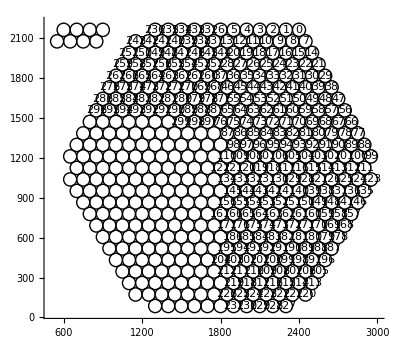

```mathematica
NNDetectorPlot[layout, Axes->True, ImageSize-> Full]
```